```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,var,soln},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=0; (* The number of coefficients *)
n=2; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
soln=NSolve[Join[eq1,eq2,eq3,eq4],var,Reals,WorkingPrecision->10];
Print["Number of variables ",Length[var]," Number of equations ",Length[Join[eq1,eq2,eq3,eq4]]," 4M+2= ",4M+2];
Print[soln];
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.05559}. NIntegrate obtained -1.18631×10^-16 and 5.42781×10^-17 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.05559}. NIntegrate obtained -1.18631×10^-16 and 5.42781×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.89606}. NIntegrate obtained -1.30104×10^-15 and 4.22719×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Number of variables 2 Number of equations 2 4M+2= 2

{{ϕ[0]→1.92623×10^-11+1.88808×10^-17 ϕ[1]}}

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,var,soln},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=1; (* The number of coefficients *)
n=2; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
soln=NSolve[Join[eq1,eq2,eq3,eq4],var,Reals,WorkingPrecision->10];
Print["Number of variables ",Length[var]," Number of equations ",Length[Join[eq1,eq2,eq3,eq4]]," 4M+2= ",4M+2];
Print[soln];
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.05559}. NIntegrate obtained -1.18631×10^-16 and 5.42781×10^-17 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.05559}. NIntegrate obtained -1.18631×10^-16 and 5.42781×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.89606}. NIntegrate obtained -1.30104×10^-15 and 4.22719×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Number of variables 6 Number of equations 6 4M+2= 6

{{ϕ[0]→1.92623×10^-11-1.23136×10^-16 C1[1]+1.88808×10^-17 ϕ[1],A1[1]→6.13683×10^-12-1. C1[1],B1[1]→2.1566×10^-12+7.28877×10^-17 C1[1],D1[1]→7.76415×10^-28}}

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,var,soln},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=3; (* The number of coefficients *)
n=2; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
soln=NSolve[Join[eq1,eq2,eq3,eq4],var,Reals,WorkingPrecision->10];
Print["Number of variables ",Length[var]," Number of equations ",Length[Join[eq1,eq2,eq3,eq4]]," 4M+2= ",4M+2];
Print[soln];
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.05559}. NIntegrate obtained -1.18631×10^-16 and 5.42781×10^-17 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.05559}. NIntegrate obtained -1.18631×10^-16 and 5.42781×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.89606}. NIntegrate obtained -1.30104×10^-15 and 4.22719×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Number of variables 14 Number of equations 14 4M+2= 14

{}

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,var,soln},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=1; (* The number of coefficients *)
n=2.01; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
soln=NSolve[Join[eq1,eq2,eq3,eq4],var,Reals,WorkingPrecision->10];
Print["Number of variables ",Length[var]," Number of equations ",Length[Join[eq1,eq2,eq3,eq4]]," 4M+2= ",4M+2];
Print[soln];
]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -7.77156×10^-16 and 3.2113×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58297}. NIntegrate obtained 8.32667×10^-17 and 8.09486×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -8.32667×10^-16 and 3.19916×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Number of variables 6 Number of equations 6 4M+2= 6

{{ϕ[0]→978.874+8.59729×10^-18 C1[1]+0.000959483 ϕ[1],A1[1]→1.72925×10^-11-1.00192 C1[1],B1[1]→-1.092×10^-11+1.3299×10^-17 C1[1],D1[1]→-8.64328×10^-29}}

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,var,soln},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=2; (* The number of coefficients *)
n=2.01; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
soln=NSolve[Join[eq1,eq2,eq3,eq4],var,Reals,WorkingPrecision->10];
Print["Number of variables ",Length[var]," Number of equations ",Length[Join[eq1,eq2,eq3,eq4]]," 4M+2= ",4M+2];
Print[soln];
]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -7.77156×10^-16 and 3.2113×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58297}. NIntegrate obtained 8.32667×10^-17 and 8.09486×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -8.32667×10^-16 and 3.19916×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Number of variables 10 Number of equations 10 4M+2= 10

{}

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,var,soln},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=0; (* The number of coefficients *)
n=2; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
soln=FindInstance[Join[eq1,eq2,eq3,eq4],var,Reals,WorkingPrecision->10];
Print["Number of variables ",Length[var]," Number of equations ",Length[Join[eq1,eq2,eq3,eq4]]," 4M+2= ",4M+2];
Print[soln];
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.05559}. NIntegrate obtained -1.18631×10^-16 and 5.42781×10^-17 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.05559}. NIntegrate obtained -1.18631×10^-16 and 5.42781×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.89606}. NIntegrate obtained -1.30104×10^-15 and 4.22719×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Number of variables 2 Number of equations 2 4M+2= 2

{{ϕ[0]→-12/5,ϕ[1]→-1.27113×10^17}}

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,var,soln},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=1; (* The number of coefficients *)
n=2; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
soln=FindInstance[Join[eq1,eq2,eq3,eq4],var,Reals,WorkingPrecision->10];
Print["Number of variables ",Length[var]," Number of equations ",Length[Join[eq1,eq2,eq3,eq4]]," 4M+2= ",4M+2];
Print[soln];
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.05559}. NIntegrate obtained -1.18631×10^-16 and 5.42781×10^-17 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.05559}. NIntegrate obtained -1.18631×10^-16 and 5.42781×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.89606}. NIntegrate obtained -1.30104×10^-15 and 4.22719×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Number of variables 6 Number of equations 6 4M+2= 6

{{ϕ[0]→1.92623×10^-11,ϕ[1]→-1/2,A1[1]→-12/5,B1[1]→2.15697×10^-12,C1[1]→2.4,D1[1]→-1.97459×10^-16}}

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,var,soln},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=2; (* The number of coefficients *)
n=2; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
soln=FindInstance[Join[eq1,eq2,eq3,eq4],var,Reals,WorkingPrecision->10,RandomSeeding->Automatic];
Print["Number of variables ",Length[var]," Number of equations ",Length[Join[eq1,eq2,eq3,eq4]]," 4M+2= ",4M+2];
Print[soln];
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.05559}. NIntegrate obtained -1.18631×10^-16 and 5.42781×10^-17 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.05559}. NIntegrate obtained -1.18631×10^-16 and 5.42781×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.89606}. NIntegrate obtained -1.30104×10^-15 and 4.22719×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-3.33067×10^-16,7.63278×10^-17,8.32667×10^-17,-5.27356×10^-16,5.16948×10^-16,-2.77556×10^-17,-7.91034×10^-16,-1.30104×10^-15,-1.18631×10^-16,6.28319,-1.21029×10^-10},«8»,{2.83801×10^-15,-2.08167×10^-17,-1.45717×10^-16,0.,3.19189×10^-16,1.04083×10^-17,9.92262×10^-16,-3.14159,0.,0.,0.}} may contain significant numerical errors.

Number of variables 10 Number of equations 10 4M+2= 10

{}

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,var,soln},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=2; (* The number of coefficients *)
n=2.01; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
soln=FindInstance[Join[eq1,eq2,eq3,eq4],var,Reals,WorkingPrecision->10];
Print["Number of variables ",Length[var]," Number of equations ",Length[Join[eq1,eq2,eq3,eq4]]," 4M+2= ",4M+2];
Print[soln];
]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -7.77156×10^-16 and 3.2113×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58297}. NIntegrate obtained 8.32667×10^-17 and 8.09486×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -8.32667×10^-16 and 3.19916×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{8.32667×10^-17,5.53377×10^-16,-1.05471×10^-15,-8.32667×10^-16,-1.38778×10^-17,8.32667×10^-17,-2.77556×10^-17,-7.77156×10^-16,-0.00602861,6.28319,-6150.45},«8»,{-5.55112×10^-17,-2.08167×10^-17,-5.55112×10^-17,0.,-3.88578×10^-16,6.93889×10^-18,7.77156×10^-16,-3.13297,0.,0.,0.}} may contain significant numerical errors.

Number of variables 10 Number of equations 10 4M+2= 10

{{ϕ[0]→-9.21997×10^-14,ϕ[1]→-1.02021×10^6,A1[1]→-1.17157×10^-42,A1[2]→-3.26366×10^-28,B1[1]→7.61451×10^-29,B1[2]→-1.02629×10^-28,C1[1]→1.10518×10^-27,C1[2]→4.56475×10^-32,D1[1]→4.46252×10^-43,D1[2]→1.21635×10^-31}}

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -5.55112×10^-16 and 5.73259×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.5707}. NIntegrate obtained 2.77556×10^-16 and 1.37531×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -6.66134×10^-16 and 5.93942×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Number of variables 14 Number of equations 14 4M+2= 14

{{ϕ[0]→-7/2,ϕ[1]→-1.02032×10^6,A1[1]→14/5,A1[2]→-3.38342×10^-17,A1[3]→0.849939,B1[1]→2.73126×10^-16,B1[2]→-9.97179×10^-17,B1[3]→9.56129×10^-16,C1[1]→-2.69996,C1[2]→9.17976×10^-17,C1[3]→-0.77786,D1[1]→-3.78876×10^-16,D1[2]→2.32961×10^-17,D1[3]→-1.05704×10^-16}}

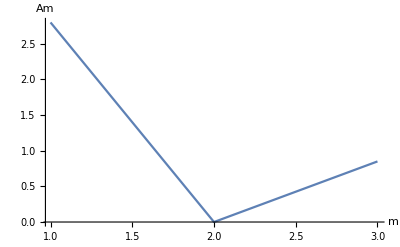

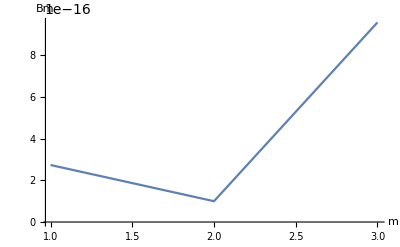

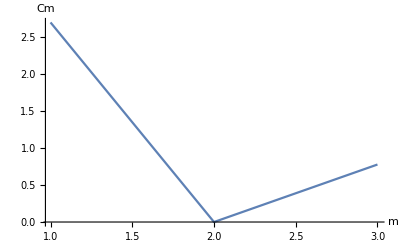

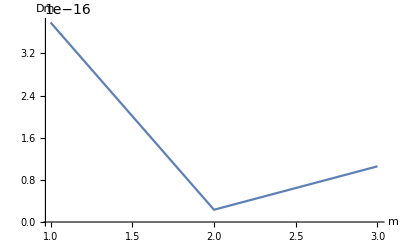

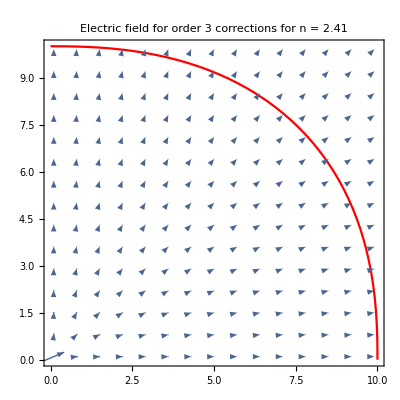

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,var,soln},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=3; (* The number of coefficients *)
n=2.41; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
soln=FindInstance[Join[eq1,eq2,eq3,eq4],var,Reals,WorkingPrecision->100,RandomSeeding->Automatic];
Print["Number of variables ",Length[var]," Number of equations ",Length[Join[eq1,eq2,eq3,eq4]]," 4M+2= ",4M+2];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[A1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,Abs[Part[B1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,Abs[Part[C1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,Abs[Part[D1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
Er[x_,y_]:=Part[-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln,1];
Et[x_,y_]:=Part[(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln,1];
Show[VectorPlot[{(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.05559}. NIntegrate obtained -1.18631×10^-16 and 5.42781×10^-17 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.05559}. NIntegrate obtained -1.18631×10^-16 and 5.42781×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.89606}. NIntegrate obtained -1.30104×10^-15 and 4.22719×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Number of variables 2 Number of equations 2 4M+2= 2

{{ϕ[0]→-11/5,ϕ[1]→-1.16521×10^17}}

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

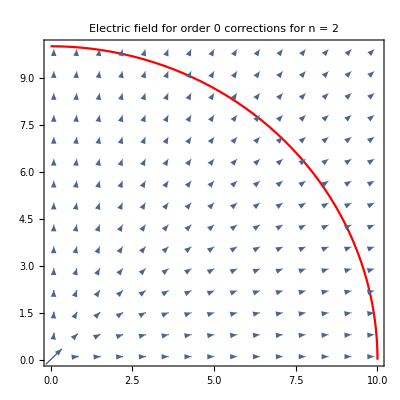

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,var,soln},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=0; (* The number of coefficients *)
n=2; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
soln=FindInstance[Join[eq1,eq2,eq3,eq4],var,Reals,WorkingPrecision->100,RandomSeeding->Automatic];
Print["Number of variables ",Length[var]," Number of equations ",Length[Join[eq1,eq2,eq3,eq4]]," 4M+2= ",4M+2];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[A1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,Abs[Part[B1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,Abs[Part[C1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,Abs[Part[D1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
Er[x_,y_]:=Part[-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln,1];
Et[x_,y_]:=Part[(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln,1];
Show[VectorPlot[{(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.05559}. NIntegrate obtained -1.18631×10^-16 and 5.42781×10^-17 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.05559}. NIntegrate obtained -1.18631×10^-16 and 5.42781×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.89606}. NIntegrate obtained -1.30104×10^-15 and 4.22719×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Number of variables 6 Number of equations 6 4M+2= 6

{{ϕ[0]→1.92623×10^-11,ϕ[1]→5,A1[1]→-27/10,B1[1]→2.15702×10^-12,C1[1]→2.7,D1[1]→-2.22142×10^-16}}

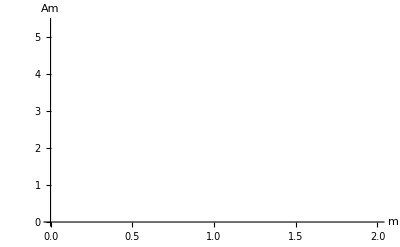

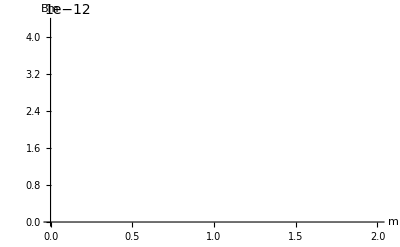

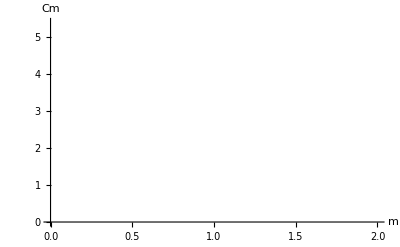

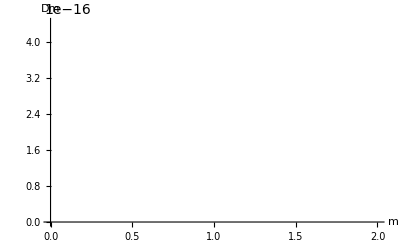

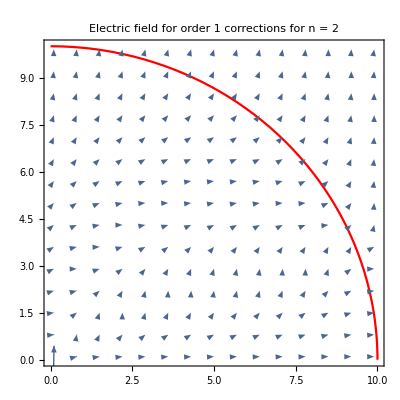

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,var,soln},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=1; (* The number of coefficients *)
n=2; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
soln=FindInstance[Join[eq1,eq2,eq3,eq4],var,Reals,WorkingPrecision->100,RandomSeeding->Automatic];
Print["Number of variables ",Length[var]," Number of equations ",Length[Join[eq1,eq2,eq3,eq4]]," 4M+2= ",4M+2];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[A1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,Abs[Part[B1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,Abs[Part[C1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,Abs[Part[D1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
Er[x_,y_]:=Part[-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln,1];
Et[x_,y_]:=Part[(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.05559}. NIntegrate obtained -1.18631×10^-16 and 5.42781×10^-17 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.05559}. NIntegrate obtained -1.18631×10^-16 and 5.42781×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.89606}. NIntegrate obtained -1.30104×10^-15 and 4.22719×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-3.33067×10^-16,7.63278×10^-17,8.32667×10^-17,-5.27356×10^-16,5.16948×10^-16,-2.77556×10^-17,-7.91034×10^-16,-1.30104×10^-15,-1.18631×10^-16,6.28319,-1.21029×10^-10},«8»,{2.83801×10^-15,-2.08167×10^-17,-1.45717×10^-16,0.,3.19189×10^-16,1.04083×10^-17,9.92262×10^-16,-3.14159,0.,0.,0.}} may contain significant numerical errors.

Number of variables 10 Number of equations 10 4M+2= 10

{}

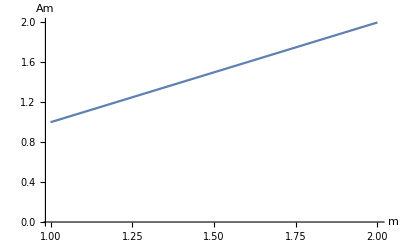

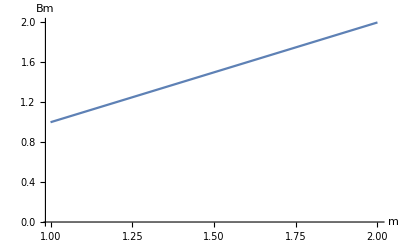

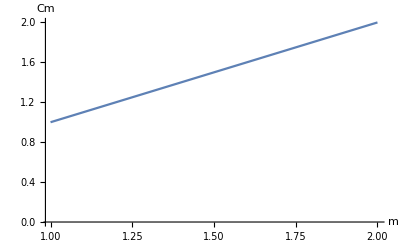

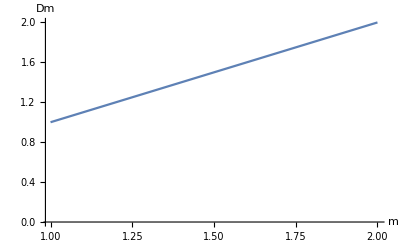

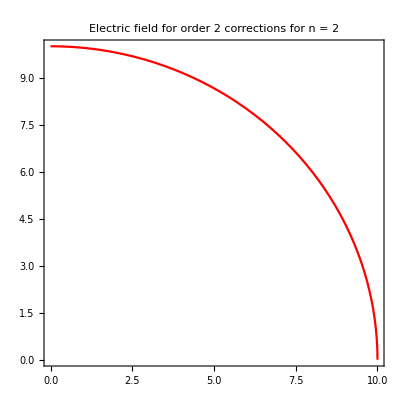

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,var,soln},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=2; (* The number of coefficients *)
n=2; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
soln=FindInstance[Join[eq1,eq2,eq3,eq4],var,Reals,WorkingPrecision->100,RandomSeeding->Automatic];
Print["Number of variables ",Length[var]," Number of equations ",Length[Join[eq1,eq2,eq3,eq4]]," 4M+2= ",4M+2];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[A1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,Abs[Part[B1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,Abs[Part[C1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,Abs[Part[D1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
Er[x_,y_]:=Part[-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln,1];
Et[x_,y_]:=Part[(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.05559}. NIntegrate obtained -1.18631×10^-16 and 5.42781×10^-17 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.05559}. NIntegrate obtained -1.18631×10^-16 and 5.42781×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.89606}. NIntegrate obtained -1.30104×10^-15 and 4.22719×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-5.13478×10^-16,-3.33067×10^-16,7.63278×10^-17,-4.05925×10^-16,8.32667×10^-17,-5.27356×10^-16,1.38778×10^-17,5.16948×10^-16,-2.77556×10^-17,-7.49401×10^-16,-7.91034×10^-16,-1.30104×10^-15,-1.18631×10^-16,6.28319,-1.21029×10^-10},«12»,{1.249×10^-15,1.77983×10^-15,4.16334×10^-17,«9»,0.,0.,0.}} may contain significant numerical errors.

Number of variables 14 Number of equations 14 4M+2= 14

{}

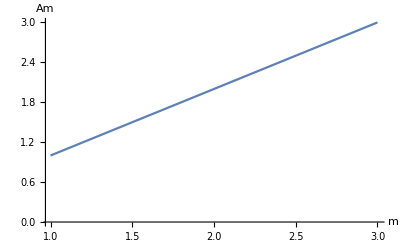

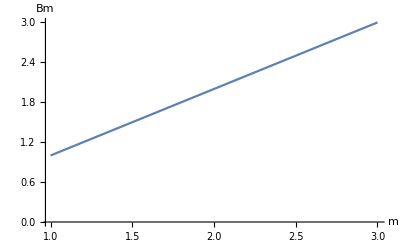

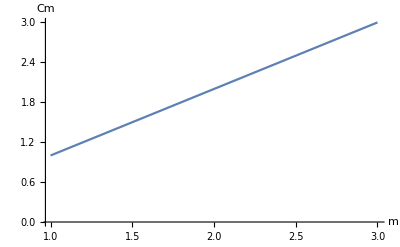

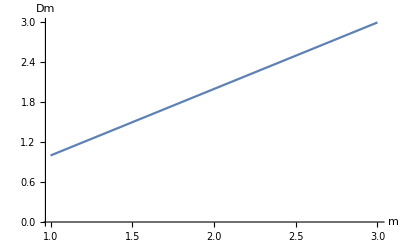

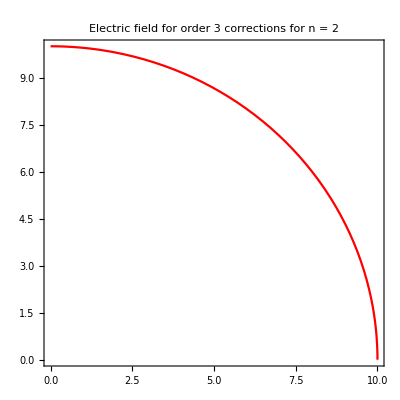

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,var,soln},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=3; (* The number of coefficients *)
n=2; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
soln=FindInstance[Join[eq1,eq2,eq3,eq4],var,Reals,WorkingPrecision->100,RandomSeeding->Automatic];
Print["Number of variables ",Length[var]," Number of equations ",Length[Join[eq1,eq2,eq3,eq4]]," 4M+2= ",4M+2];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[A1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,Abs[Part[B1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,Abs[Part[C1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,Abs[Part[D1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
Er[x_,y_]:=Part[-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln,1];
Et[x_,y_]:=Part[(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln,1];
Show[VectorPlot[{Abs[(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2]],Abs[(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -7.77156×10^-16 and 3.2113×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58297}. NIntegrate obtained 8.32667×10^-17 and 8.09486×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -8.32667×10^-16 and 3.19916×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Number of variables 2 Number of equations 2 4M+2= 2

{{ϕ[0]→23/5,ϕ[1]→-1.01542×10^6}}

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

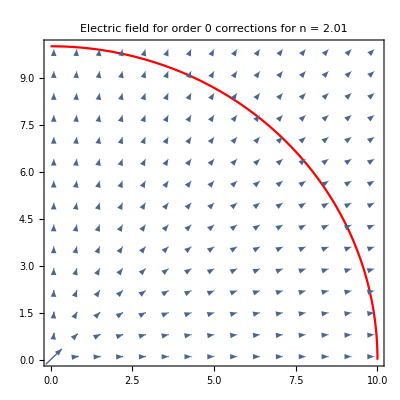

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,var,soln},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=0; (* The number of coefficients *)
n=2.01; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
soln=FindInstance[Join[eq1,eq2,eq3,eq4],var,Reals,WorkingPrecision->100,RandomSeeding->Automatic];
Print["Number of variables ",Length[var]," Number of equations ",Length[Join[eq1,eq2,eq3,eq4]]," 4M+2= ",4M+2];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[A1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,Abs[Part[B1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,Abs[Part[C1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,Abs[Part[D1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
Er[x_,y_]:=Part[-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln,1];
Et[x_,y_]:=Part[(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln,1];
Show[VectorPlot[{(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -7.77156×10^-16 and 3.2113×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58297}. NIntegrate obtained 8.32667×10^-17 and 8.09486×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -8.32667×10^-16 and 3.19916×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Number of variables 6 Number of equations 6 4M+2= 6

{{ϕ[0]→11/10,ϕ[1]→-1.01906×10^6,A1[1]→-3/10,B1[1]→-1.2268×10^-14,C1[1]→0.299425,D1[1]→6.62616×10^-19}}

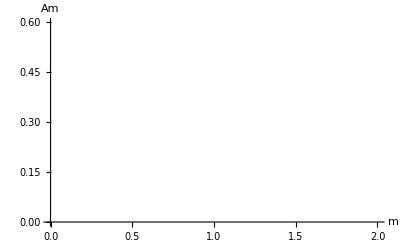

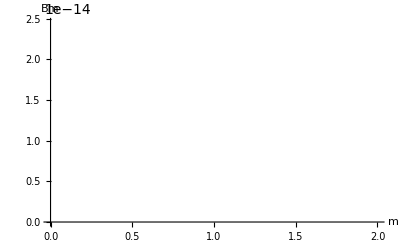

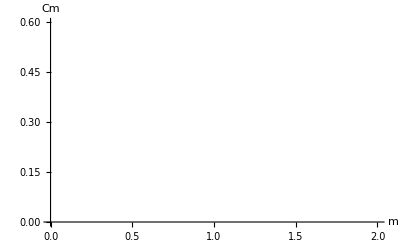

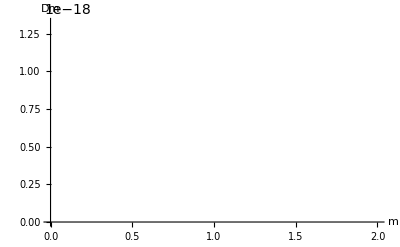

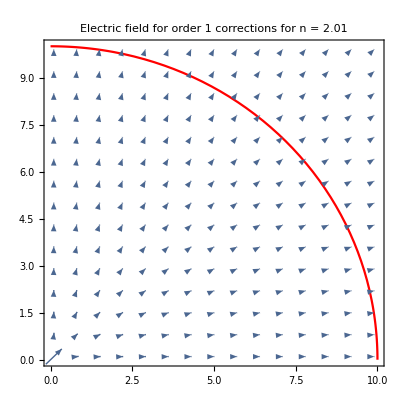

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,var,soln},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=1; (* The number of coefficients *)
n=2.01; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
soln=FindInstance[Join[eq1,eq2,eq3,eq4],var,Reals,WorkingPrecision->100,RandomSeeding->Automatic];
Print["Number of variables ",Length[var]," Number of equations ",Length[Join[eq1,eq2,eq3,eq4]]," 4M+2= ",4M+2];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[A1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,Abs[Part[B1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,Abs[Part[C1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,Abs[Part[D1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
Er[x_,y_]:=Part[-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln,1];
Et[x_,y_]:=Part[(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln,1];
Show[VectorPlot[{(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -7.77156×10^-16 and 3.2113×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58297}. NIntegrate obtained 8.32667×10^-17 and 8.09486×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -8.32667×10^-16 and 3.19916×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{8.32667×10^-17,5.53377×10^-16,-1.05471×10^-15,-8.32667×10^-16,-1.38778×10^-17,8.32667×10^-17,-2.77556×10^-17,-7.77156×10^-16,-0.00602861,6.28319,-6150.45},«8»,{-5.55112×10^-17,-2.08167×10^-17,-5.55112×10^-17,0.,-3.88578×10^-16,6.93889×10^-18,7.77156×10^-16,-3.13297,0.,0.,0.}} may contain significant numerical errors.

Number of variables 10 Number of equations 10 4M+2= 10

{{ϕ[0]→-9.21997×10^-14,ϕ[1]→-1.02021×10^6,A1[1]→-1.17157×10^-42,A1[2]→-3.26366×10^-28,B1[1]→7.61451×10^-29,B1[2]→-1.02629×10^-28,C1[1]→1.10518×10^-27,C1[2]→4.56475×10^-32,D1[1]→4.46252×10^-43,D1[2]→1.21635×10^-31}}

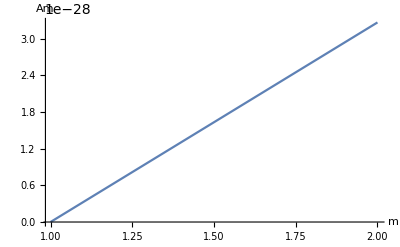

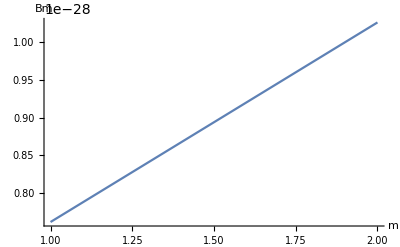

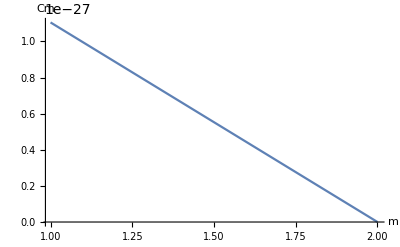

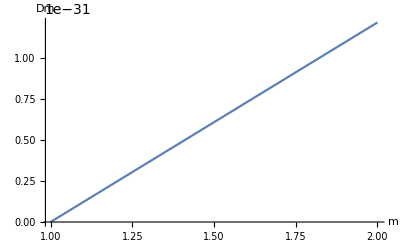

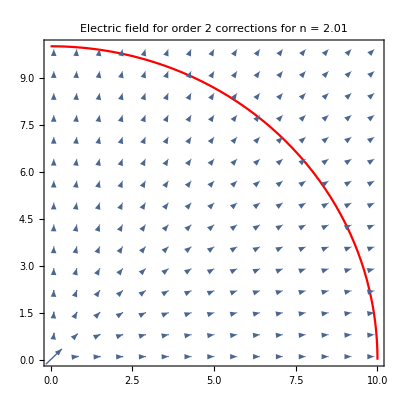

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,var,soln},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=2; (* The number of coefficients *)
n=2.01; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
soln=FindInstance[Join[eq1,eq2,eq3,eq4],var,Reals,WorkingPrecision->100,RandomSeeding->Automatic];
Print["Number of variables ",Length[var]," Number of equations ",Length[Join[eq1,eq2,eq3,eq4]]," 4M+2= ",4M+2];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[A1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,Abs[Part[B1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,Abs[Part[C1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,Abs[Part[D1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
Er[x_,y_]:=Part[-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln,1];
Et[x_,y_]:=Part[(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln,1];
Show[VectorPlot[{(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -7.77156×10^-16 and 3.2113×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.58297}. NIntegrate obtained 8.32667×10^-17 and 8.09486×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.15377}. NIntegrate obtained -8.32667×10^-16 and 3.19916×10^-13 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{-3.33067×10^-16,8.32667×10^-17,5.53377×10^-16,-6.66134×10^-16,-1.05471×10^-15,-8.32667×10^-16,-1.17961×10^-16,-1.38778×10^-17,8.32667×10^-17,-8.18789×10^-16,-2.77556×10^-17,-7.77156×10^-16,-0.00602861,6.28319,-6150.45},«12»,{-8.11851×10^-16,1.29063×10^-15,4.16334×10^-17,6.5727×10^-16,«8»,0.,0.,0.}} may contain significant numerical errors.

Number of variables 14 Number of equations 14 4M+2= 14

{{ϕ[0]→-9.57539×10^-14,ϕ[1]→-1.02021×10^6,A1[1]→4/5,A1[2]→3.43776×10^-17,A1[3]→0.26607,B1[1]→2.23671×10^-17,B1[2]→-1.56968×10^-17,B1[3]→8.86761×10^-17,C1[1]→-0.799127,C1[2]→2.28592×10^-17,C1[3]→-0.265205,D1[1]→-4.0959×10^-17,D1[2]→-3.25057×10^-17,D1[3]→-2.27641×10^-17}}

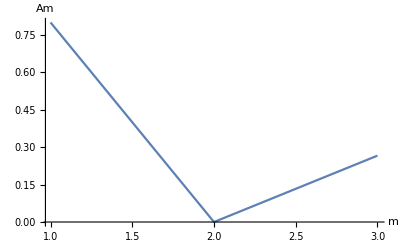

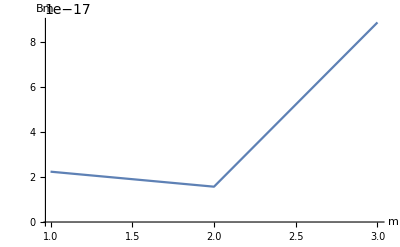

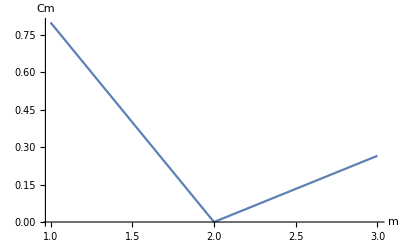

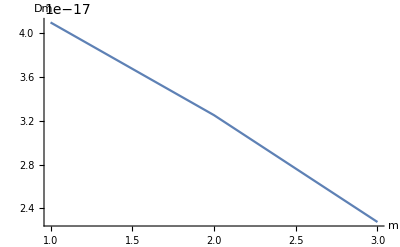

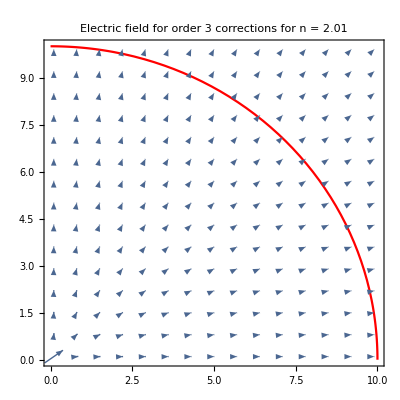

```mathematica
Block[
{R,Er,Et,func,q,ϵ0,M,n,m,k,I1,I2,I3,I4,I5,I6,I7,I8,I9,I10,A1,B1,C1,D1,ϕ,eq1,eq2,eq3,eq4,var,soln},
q=5.673*10^(-5);(* The linear charge density *)
ϵ0=8.85*10^(-12);(* Permittivity of free space *)
M=3; (* The number of coefficients *)
n=2.01; (* Curvature exponents *)
R=10;(* The range of the stretch of the conveyor belt *)
I1=<||>;I2=<||>;I3=<||>;I4=<||>;I5=<||>;
I6=<||>;I7=<||>;I8=<||>;I9=<||>;I10=<||>;
func[θ_,n_]:=If[0≤θ≤π/2,Cos[θ](1+Tan[θ]^n)^(1/n),If[π/2≤θ≤π,func[π-θ,n],If[π≤θ≤3π/2,func[θ-π,n],func[2π-θ,n]]]];
For[
k=0,k≤M,k++,
For[
m=0,m≤M+1,m++,
I1=Append[I1,k->NIntegrate[Log[func[θ,n]]Cos[k θ],{θ,0,2π}]];
I2=Append[I2,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I3=Append[I3,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I4=Append[I4,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Cos[k θ],{θ,0,2π}]];
I5=Append[I5,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Cos[k θ],{θ,0,2π}]];
I6=Append[I6,k->NIntegrate[Log[func[θ,n]]Sin[k θ],{θ,0,2π}]];
I7=Append[I7,{m,k}->NIntegrate[func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I8=Append[I8,{m,k}->NIntegrate[func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
I9=Append[I9,{m,k}->NIntegrate[1/func[θ,n]^m Cos[m θ]Sin[k θ],{θ,0,2π}]];
I10=Append[I10,{m,k}->NIntegrate[1/func[θ,n]^m Sin[m θ]Sin[k θ],{θ,0,2π}]];
]
];
eq1=Table[2π DiscreteDelta[k]ϕ[0]+(ϕ[1]+q/(2π ϵ0))I1[k]+Sum[A1[m]I2[{m,k}]+B1[m]I3[{m,k}]+C1[m]I4[{m,k}]+D1[m]I5[{m,k}],{m,1,M}]==0,{k,0,M}];
eq2=Table[Sum[m B1[m]I2[{m+1,k}]-m A1[m]I3[{m+1,k}]+m D1[m]I4[{m-1,k}]-m C1[m]I5[{m-1,k}],{m,1,M}]==0,{k,0,M}];
eq3=Table[(ϕ[1]+q/(2π ϵ0))I6[k]+Sum[A1[m]I7[{m,k}]+B1[m]I8[{m,k}]+C1[m]I9[{m,k}]+D1[m]I10[{m,k}],{m,1,M}]==0,{k,1,M}];
eq4=Table[Sum[m B1[m]I7[{m+1,k}]-m A1[m]I8[{m+1,k}]+m D1[m]I9[{m-1,k}]-m C1[m]I10[{m-1,k}],{m,1,M}]==0,{k,1,M}];
var=Join[{ϕ[0],ϕ[1]},Table[A1[m],{m,1,M}],Table[B1[m],{m,1,M}],Table[C1[m],{m,1,M}],Table[D1[m],{m,1,M}]];
soln=FindInstance[Join[eq1,eq2,eq3,eq4],var,Reals,WorkingPrecision->100,RandomSeeding->Automatic];
Print["Number of variables ",Length[var]," Number of equations ",Length[Join[eq1,eq2,eq3,eq4]]," 4M+2= ",4M+2];
Print[soln];
Print[ListLinePlot[Table[{m,Abs[Part[A1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Am"}]];
Print[ListLinePlot[Table[{m,Abs[Part[B1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Bm"}]];
Print[ListLinePlot[Table[{m,Abs[Part[C1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Cm"}]];
Print[ListLinePlot[Table[{m,Abs[Part[D1[m]/.soln,1]]},{m,1,M}],PlotRange->All,AxesLabel->{"m","Dm"}]];
Er[x_,y_]:=Part[-(ϕ[1]/Sqrt[x^2+y^2]+1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(A1[m]Cos[m ArcTan[x,y]]+B1[m]Sin[m ArcTan[x,y]])-m(Sqrt[x^2+y^2]/R)^(m-1)(C1[m]Cos[m ArcTan[x,y]]+D1[m]Sin[m ArcTan[x,y]]),{m,1,M}])/.soln,1];
Et[x_,y_]:=Part[(1/R Sum[m(R/Sqrt[x^2+y^2])^(m+1)(-A1[m]Sin[m ArcTan[x,y]]+B1[m]Cos[m ArcTan[x,y]])+m(Sqrt[x^2+y^2]/R)^(m-1)(-C1[m]Sin[m ArcTan[x,y]]+D1[m]Cos[m ArcTan[x,y]]),{m,1,M}])/.soln,1];
Show[VectorPlot[{(Er[x,y] x-Et[x,y] y)/Sqrt[x^2+y^2],(Er[x,y] y+Et[x,y] x)/Sqrt[x^2+y^2]},{x,0.01R,0.99R},{y,0.01R,0.99R},VectorScale->{0.05,1,Automatic}],PolarPlot[R Sec[θ]/(1+Tan[θ]^n)^(1/n),{θ,0,π/2},PlotStyle->Red],PlotRange->{{0,R},{0,R}},PlotLabel->StringJoin["Electric field for order ",ToString[M]," corrections for n = ",ToString[n]]]
]
```